```mathematica
imgs=Table[Table[{0,0,1,N[(1+Cos[(Sqrt[x^2+y^2]-2i)])/2 Exp[-Sqrt[x^2+y^2]/5] Exp[-i/4]]},{x,-32,31},{y,-32,31}],{i,0,8}];
```

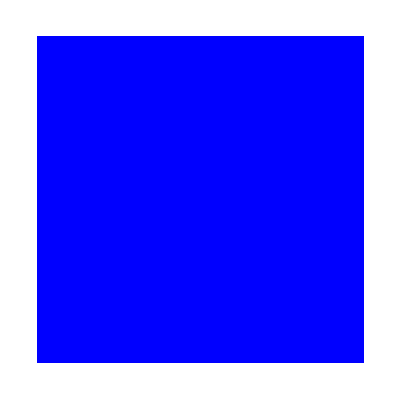
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Show[Graphics[Raster[#]]]&,imgs]
```

```mathematica
MapIndexed[Export[StringJoin["d:\\kryss\\test\\styletest\\circ_",ToString[#2[[1]]],".png"],Graphics[Raster[#]],"PNG",Background->None ,ImageSize->{64,64}]&,imgs]
```

{d:\kryss\test\styletest\circ_1.png,d:\kryss\test\styletest\circ_2.png,d:\kryss\test\styletest\circ_3.png,d:\kryss\test\styletest\circ_4.png,d:\kryss\test\styletest\circ_5.png,d:\kryss\test\styletest\circ_6.png,d:\kryss\test\styletest\circ_7.png,d:\kryss\test\styletest\circ_8.png,d:\kryss\test\styletest\circ_9.png}